## Piezo driver noise analysis

Useful references: 
* http://www.ti.com/lit/an/sboa066a/sboa066a.pdf
* http://www.ti.com/lit/an/slva043b/slva043b.pdf

### Preliminaries/Constants

```mathematica
(* import and configure MaTeX, for using latex in mathematica plots *)
<<MaTeX`
ConfigureMaTeX["pdfLaTeX"->"/usr/texbin/pdflatex","Ghostscript"->"/usr/local/Cellar/ghostscript/9.16/bin/gs"];
SetOptions[MaTeX,"Preamble"->{"\\usepackage{amsmath,amssymb} \\usepackage{siunitx} \\DeclareSIUnit{\\sqrthz}{\\ensuremath{\\sqrt{\\text{\\hertz}}}}","\\usepackage{color,txfonts}"}];

texStyle={FontFamily->"Latin Modern Roman",FontSize->16};

(* keep mathematica from complaining in interpolating functions *)
Off[InterpolatingFunction::dmval]

(* set directory path *)
SetDirectory[NotebookDirectory[]];

(* constants, etc. *)
c=299792458;
kB=1.38064852*^-23;
hbar=1.0545718*^-34;
ϵ0=8.85418782*^-12;
a0=.52917721092*^-10;
e=1.602176487*^-19;
pp=1.*^-12;
nn=1.*^-9;
uu=1.*^-6;
mm=1.*^-3;
kk=1.*^3;
MM=1.*^6;
GG=1.*^9;

(* parallel impedances *)
par[z1_,z2_]:=z1 z2/(z1+z2);
```

### LM7171

The LM7171 is a very high speed, high slew-rate op amp.

```mathematica
OLG:=10.^(85/20); (* open loop gain, = 85dB *)
SR:=4100/uu (*slew rate, V/us*)
Vos:=0.2 mm (* Input offset voltage *)
VosTc:=35uu(*input offset voltage drift, V/degC*)
Ib:=2.7uu (* input bias current *)
Ios:=0.1uu (* input offset current *)
CMRR:=10.^(105/20) (* = 105dB, common mode rejection ratio *)
PSRR:=10.^(90/20) (* = 90dB, power supply rejection ratio *)
en:=14nn (* @10kHz, input-referred voltage noise, V/√Hz *)
in:=1.5pp (* @10kHz, input-referred current noise, A/√Hz *)
VnDAC:=100nn (* @ 1 kHz, conservative @ 10kHz; dac noise *)
```

#### Noise import

```mathematica
VnoiseImg=Binarize[Import["LM7171VoltNoise.png"]]
```

-Graphics-

Pull points off graph. {vy, vx, vo} are the coordinates of the y, x, and origin (axes), for coordinate transformation.
Vcurve is a sequence of points from the curve itself.
To get these off the graph, double click and select “coordinates tool”.
From that list of pixel coordinates, do a transformation to get into units of nV/rtHz.

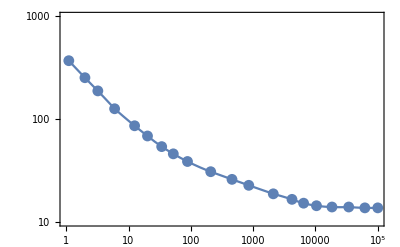

```mathematica
{vy,vx,vo}={{240,16},{723,499},{240,499}};
Vcurve={{723,466},{703,466},{678,464},{652,464},{628,461},{608,455},{590,446},{561,433},{523,413},{497,399},{464,381},{428,357},{406,339},{388,322},{366,297},{346,273},{315,233},{289,191},{269,160},{244,120}};

(* coordinate transformation; working in log units *)
Vtransform=FindGeometricTransform[{{0,1},{5,1},{0,3}},{vo,vx,vy}][[2]];
VptsLog=Vtransform@Vcurve;
Vpts=Map[10^#&,VptsLog,{2}];
(* VinterpolationLog is the voltage noise interpolating function *)
VinterpolationLog=Interpolation[VptsLog,InterpolationOrder->2];

(* plot along with extracted points to make sure the interpolation worked ok *)
Vplt=ListLogLogPlot[Vpts,PlotRange->{{1,100000},{10,1000}},Frame->True,GridLines->Automatic];
Show[Vplt,LogLogPlot[10^VinterpolationLog[Log10[x]],{x,1,10^5}]]
```

Now, we do the same thing with the current noise:

```mathematica
InoiseImg=Binarize[Import["LM7171CurrNoise.png"]]
```

-Graphics-

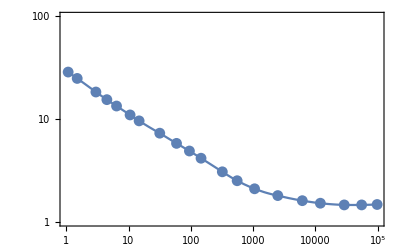

```mathematica
{iy,ix,io}={{184,9},{667,493},{184,493}};
Icurve={{666,452},{642,453},{615,453},{578,449},{550,443},{512,431},{476,415},{449,396},{426,375},{393,343},{375,326},{355,308},{329,284},{297,255},{283,241},{262,220},{247,205},{230,187},{201,155},{187,140}};
(* coordinate transformation; working in log units *)
Itransform=FindGeometricTransform[{{0,0},{5,0},{0,2}},{io,ix,iy}][[2]];
IptsLog=Itransform@Icurve;
Ipts=Map[10^#&,IptsLog,{2}];
IinterpolationLog=Interpolation[IptsLog,InterpolationOrder->2];
Iplt=ListLogLogPlot[Ipts,PlotRange->{{1,100000},{1,100}},Frame->True,GridLines->Automatic];
Show[Iplt,LogLogPlot[10^IinterpolationLog[Log10[x]],{x,1,10^5}]]
```

And one more time for the DAC noise:

```mathematica
DacNoiseImg=Binarize[Import["AD5663RVoltNoise.png"]]
```

-Graphics-

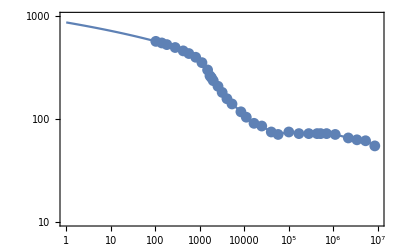

```mathematica
{dy,dx,do}={{155,48},{903,645},{155,645}};
DACcurve={{893,604},{862,599},{833,598},{804,596},{760,592},{731,591},{711,591},{699,591},{671,591},{638,591},{604,589},{568,592},{545,589},{513,581},{487,577},{461,567},{443,557},{413,540},{396,527},{380,509},{366,489},{350,468},{344,456},{339,448},{331,420},{312,380},{291,346},{268,320},{249,300},{222,273},{194,248},{177,233},{157,218}};
(*coordinate transformation;working in log units only in x*)DACtransform=FindGeometricTransform[{{2,0},{7,0},{2,800}},{do,dx,dy}][[2]];
DACptsLog=DACtransform@DACcurve;
DACpts=Map[{10^#[[1]],#[[2]]}&,DACptsLog];
DACinterpolationLog=Interpolation[DACptsLog,InterpolationOrder->1];
DACplt=ListLogLogPlot[DACpts,PlotRange->{{1,10^7},{10,1000}},Frame->True,GridLines->Automatic];
Show[DACplt,LogLogPlot[DACinterpolationLog[Log10[x]],{x,1,10^7}]]
```

### Noise analysis

We have the following op amp model:

```mathematica
Clear[s];
R1=1MM;
C1=1nn;
R2=20.5kk;
Rmod=1MM;
Cmod=1nn;

Rlp=20.5kk;
Zlp=par[par[(1/(s 10uu)+0.7),1/(s 47nn)],1MM];(* effective Z -- see full circuit for details -- Ron resistance is 0.7 ohms for part*)

Z1=par[R1,1/(C1 s)];
Z2 = R2;
Zmod = par[Rmod, 1/(Cmod s)];

(* impedance seen at non-inverting node *)
Zp=par[Rlp,Zlp];
(* impedance seen at inverting node *)
Zn=par[par[Z2,Zmod],Z1];

NG=1+Z1/(par[Z2,Zmod]); (* noise gain *)
Ginv=Z1/par[Z2,Zmod]; (* gain at inverting input node *)
Gmod=Z1/Zmod;(* modulation gain *)
Gdc=Zlp/(Rlp+Zlp)(1+Z1/(par[Z2, Zmod])) ;(* LP filter * non-inverting gain*)
```

Now, actually compute noise as a function of frequency:

```mathematica
Zp//FullSimplify
```

(3.03951×10^12+2.12766×10^7 s)/(1.51308×10^8+s (3.05391×10^7+1. s))

```mathematica
Abs[Zp/.s->I w]//FullSimplify
```

4.3617×10^17 Abs[((0.-6.96864×10^-6 ⅈ)+4.87805×10^-11 w)/(-1.51308×10^8+w ((0.-3.05391×10^7 ⅈ)+1. w))]

```mathematica
T=300;(* assume temperatures computed at 300K *)
JohnsonNoise=NG(4 kB T (Re[Zn] +Re[Zp] ))^(1/2);(* Johnson noise *)


(* construct noise gain, impedances, etc. as functions *)
NoiseGain[s_]=NG//FullSimplify;
ZZp[s_]=Zp//FullSimplify;
ZZn[s_]=Zn//FullSimplify;

GDCInp[s_]=Gdc//FullSimplify;

(* compute the current, voltage, DAC noise. The Johnson noise is contributed directly at the output. be careful about angular vs real frequency units!
Now, here, s is a real frequency (easier for plotting, also what interpolating functions use).
 *)
JJNoise[f_]=(JohnsonNoise/.s->2Pi I f)//FullSimplify;
CurrNoiseOpAmp[f_]:=Abs[NoiseGain[2Pi I f]]( 10^(IinterpolationLog[Log10[f]])pp)√(Abs[ZZp[2Pi I f]]^2+Abs[ZZn[2Pi I f]]^2);
VoltNoiseOpAmp[f_]:=Abs[NoiseGain[2Pi I f]]( 10^(VinterpolationLog[Log10[f]])nn);
DacNoise[f_]:=Abs[GDCInp[2Pi I f]] (DACinterpolationLog[Log10[f]]nn);

(* total noise is added in quadrature; again now s is real freq *)
TotalNoise[f_]:=√(CurrNoiseOpAmp[f]^2+VoltNoiseOpAmp[f]^2+JJNoise[f]^2+DacNoise[f]^2);
```

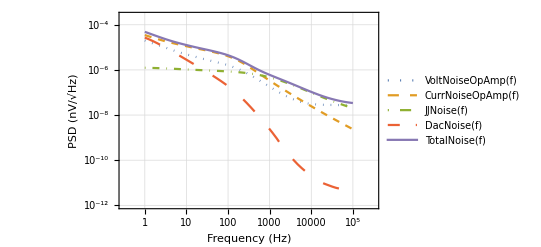

```mathematica
(* plot vs frequency for reference *)
LogLogPlot[{VoltNoiseOpAmp[f],CurrNoiseOpAmp[f],JJNoise[f],DacNoise[f],TotalNoise[f]},{f,1,100kk},Frame->True,GridLines->Automatic,PlotLegends->"Expressions",PlotStyle->{Directive[Thick,Dotted],Directive[Thick,Dashed],Directive[Thick,DotDashed],Directive[Thick,Dashing[{.03,.04}]],Thick},FrameLabel->{Style["Frequency (Hz)",{Black,FontSize->15}], Style["PSD (nV/√Hz)",{Black,FontSize->15}]}]

(* styling for publication plot *)
(*publicationPlot=LogLogPlot[{VoltNoiseOpAmp[s],CurrNoiseOpAmp[s],JJNoise[s],DacNoise[s],TotalNoise[s]},{s,1,100kk},PlotRange->{{1,100kk},{10^-12,10^-4}},Frame->True,GridLines->Automatic,PlotStyle->{Directive[Thick,Dotted],Directive[Thick,Dashed],Directive[Thick,DotDashed],Directive[Thick,Dashing[{.03,.04}]],Thick},FrameLabel->{MaTeX["\\text{Frequency} \\left(\\text{Hz}\\right)"],MaTeX["\\text{PSD}\,\,\\left(\\si[per-mode=symbol]{\\volt\\per\\sqrthz}\,\\right)"],Null,""},BaseStyle->texStyle];*)
(*Export[ParentDirectory[NotebookDirectory[]]<>"/fig/NoiseContrib.pdf",ImportString@ExportString[publicationPlot,"EPS"]]*)
```

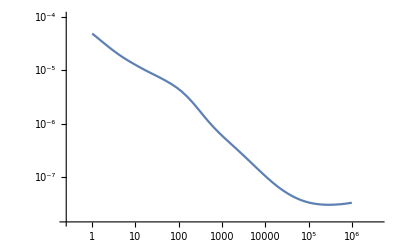

```mathematica
LogLogPlot[TotalNoise[f],{f,1,1000kk}]
```

```mathematica
exportTable=Table[{w,VoltNoiseOpAmp[w],CurrNoiseOpAmp[ w],JJNoise[w],DacNoise[w],TotalNoise[w]}/.w->10^s,{s,0,5,.05}];
Export["CalcNoiseContrib.csv",exportTable]
```

CalcNoiseContrib.csv

```mathematica
Print["Opamp voltage noise, 1Hz-100kHz: ",√NIntegrate[VoltNoiseOpAmp[s]^2,{s,1,10^5}]/uu, " uVrms"]
Print["Opamp current noise, 1Hz-100kHz: ",√NIntegrate[CurrNoiseOpAmp[ s]^2,{s,1,10^5}]/uu," uVrms"]
Print["DAC voltage noise, 1Hz-100kHz: ",√NIntegrate[DacNoise[ s]^2,{s,1,10^5}]/uu, "uVrms"]
Print["Johnson noise, 1Hz-100kHz: ",√NIntegrate[JJNoise[s]^2,{s,1,10^5}]/uu, " uVrms"]
Print["Total noise, 1Hz-100kHz: ",√NIntegrate[TotalNoise[s]^2,{s,1,10^5}]/uu, " uVrms"];
```

Opamp voltage noise, 1Hz-100kHz: 41.0172 uVrms

Opamp current noise, 1Hz-100kHz: 89.516 uVrms

DAC voltage noise, 1Hz-100kHz: 28.9893uVrms

Johnson noise, 1Hz-100kHz: 31.1512 uVrms

Total noise, 1Hz-100kHz: 107.267 uVrms

```mathematica
Print["Opamp voltage noise, 1Hz-10Hz: ",√NIntegrate[VoltNoiseOpAmp[s]^2,{s,1,10}]/uu, " uVrms"]
Print["Opamp current noise, 1Hz-10Hz: ",√NIntegrate[CurrNoiseOpAmp[ s]^2,{s,1,10}]/uu," uVrms"]
Print["DAC voltage noise, 1Hz-10Hz: ",√NIntegrate[DacNoise[ s]^2,{s,1,10}]/uu, "uVrms"]
Print["Johnson noise, 1Hz-10Hz: ",√NIntegrate[JJNoise[s]^2,{s,1,10}]/uu, " uVrms"]
Print["Total noise, 1Hz-10Hz: ",√NIntegrate[TotalNoise[s]^2,{s,1,10}]/uu, " uVrms"];
```

Opamp voltage noise, 1Hz-10Hz: 26.3067 uVrms

Opamp current noise, 1Hz-10Hz: 51.2959 uVrms

DAC voltage noise, 1Hz-10Hz: 27.8791uVrms

Johnson noise, 1Hz-10Hz: 3.37207 uVrms

Total noise, 1Hz-10Hz: 64.1243 uVrms

```mathematica
Print["Opamp voltage noise, 10Hz-100kHz: ",√NIntegrate[VoltNoiseOpAmp[s]^2,{s,10,10^5}]/uu, " uVrms"]
Print["Opamp current noise, 10Hz-100kHz: ",√NIntegrate[CurrNoiseOpAmp[ s]^2,{s,10,10^5}]/uu," uVrms"]
Print["DAC voltage noise, 10Hz-100kHz: ",√NIntegrate[DacNoise[ s]^2,{s,10,10^5}]/uu, "uVrms"]
Print["Johnson noise, 10Hz-100kHz: ",√NIntegrate[JJNoise[s]^2,{s,10,10^5}]/uu, " uVrms"]
Print["Total noise, 10Hz-100kHz: ",√NIntegrate[TotalNoise[s]^2,{s,10,10^5}]/uu, " uVrms"];
```

Opamp voltage noise, 10Hz-100kHz: 31.4702 uVrms

Opamp current noise, 10Hz-100kHz: 73.3611 uVrms

DAC voltage noise, 10Hz-100kHz: 7.9458uVrms

Johnson noise, 10Hz-100kHz: 30.9681 uVrms

Total noise, 10Hz-100kHz: 85.9906 uVrms

```mathematica
√(86^2+64.^2)
```

107.201

Finally, a few auxiliary calculations:

```mathematica
(* transfer function of low-pass filter on DAC *)
Zlp/(Rlp+Zlp)//FullSimplify//Factor
```

(1037.88 (142857.+1. s))/((4.95459+1. s) (3.0539×10^7+1. s))

This has a zero at roughly 23kHz:

```mathematica
142857.1428571429/(2Pi)
```

22736.4

```mathematica
Gdc//FullSimplify
```

(7.52917×10^12+s (3.49242×10^8+2075.77 s))/(1.51308×10^11+s (3.06904×10^10+s (3.05401×10^7+1. s)))

```mathematica
OLG
```

17782.8

```mathematica
Z1
```

(1.×10^15)/((1.×10^6+(1.×10^9)/s) s)

```mathematica
par[R2,Zmod]/(Z1+par[R2,Zmod])//FullSimplify
```

0.5-12195.1/(25390.2+1. s)

```mathematica
NMinimize[1/(1+OLG/(1+s/(10kk 2 Pi)) par[R2,Zmod]/(Z1+par[R2,Zmod])),s]
```

{0.000293276,{s→37834.2}}

```mathematica
2Pi  37834.18499328932
```

237719.

```mathematica
ZZ=par[1MM,1/(s cc)]
```

(1.×10^6)/(cc (1.×10^6+1/(cc s)) s)

```mathematica
ZZ
```

(1.×10^6 cc)/(1.×10^6+cc)

```mathematica
Zmod
```

(1.×10^15)/((1.×10^6+(1.×10^9)/s) s)

```mathematica
OLG/(1+s/(10kk 2 Pi)) par[R2,ZZ]/(ZZ+par[R2,ZZ])/.s->2Pi I f//FullSimplify
```

```mathematica
Manipulate[LogLogPlot[Abs[(-14.151097915311695-(0.+8.891397050194612*^7 ⅈ) cc f)/(((0.-10000. ⅈ)+1. f) ((0.-4.040982823382025*^-6 ⅈ)+1. cc f))],{f,.001,100000kk}],{cc,1pp,1uu}]
```

```mathematica
300*50.
```

15000.

```mathematica
10^(85/20.)
```

17782.8

```mathematica
1/(1+OLG/(1+s/(10kk 2 Pi)) par[R2,ZZ]/(ZZ+par[R2,ZZ]))/.s->2Pi I f//FullSimplify
```

(-0.0404098+f ((0.-4.04098×10^-6 ⅈ)+cc ((0.-10000. ⅈ)+1. f)))/(-14.1915+f ((0.-4.04098×10^-6 ⅈ)+cc ((0.-8.8924×10^7 ⅈ)+1. f)))

```mathematica
((0.-3.5022889438806836*^12 ⅈ)-(0.+3.5118950918153618*^6 ⅈ) cc+39385.20653218059 f+1. cc f+(0.+3.501895091815362*^12 ⅈ)+(0.+3.5018950918153618*^6 ⅈ) cc)/((0.-3.5022889438806836*^12 ⅈ)-(0.+3.5118950918153618*^6 ⅈ) cc+39385.20653218059 f+1. cc f)
```

```mathematica
((0.-3.9385206532177734*^8 ⅈ)-(0.+10000. ⅈ) cc+39385.20653218059 f+1. cc f)/((0.-3.5022889438806836*^12 ⅈ)-(0.+3.5118950918153618*^6 ⅈ) cc+39385.20653218059 f+1. cc f)//Chop
```

((0.-3.93852×10^8 ⅈ)-(0.+10000. ⅈ) cc+39385.2 f+1. cc f)/((0.-3.50229×10^12 ⅈ)-(0.+3.5119×10^6 ⅈ) cc+39385.2 f+1. cc f)

```mathematica
Manipulate[LogLogPlot[Abs[(-0.04040982823382026+f ((0.-4.040982823382025*^-6 ⅈ)+cc ((0.-10000. ⅈ)+1. f)))/(-14.191507743545516+f ((0.-4.040982823382025*^-6 ⅈ)+cc ((0.-8.892397050194612*^7 ⅈ)+1. f)))],{f,1,10000MM},PlotRange->{All,{10^-4,1}}],{{cc, 1nn},1pp,10000pp}]
```

```mathematica
ClearAll[makeReal];
makeReal[a__Symbol]:=(#/:Conjugate[#]:=#)&/@List[a]
makeReal[f]
```

{Null}

```mathematica
1+(par[R2,Zmod])/Z1//Factor
```

(2. (25390.2+1. s))/(49780.5+1. s)

```mathematica
49780.487804878045/(2Pi)
```

7922.81

```mathematica
(30 2.7/(15+2.7))-15
```

-10.4237

```mathematica
10^(85/20.)
```

17782.8

```mathematica
(-4.040982823382025*^7+f ((0.-14040.982823382024 ⅈ)+1. f))/(-1.4191507743545517*^10+f ((0.-8.892801148476952*^7 ⅈ)+1. f))Conjugate[(-4.040982823382025*^7+f ((0.-14040.982823382024 ⅈ)+1. f))/(-1.4191507743545517*^10+f ((0.-8.892801148476952*^7 ⅈ)+1. f))]//ExpandAll//Simplify
```

```mathematica
(1.6329542178868565*^15+1.1632954217886853*^8 f^2+1. f^4)/(2.0139889203511237*^20+7.908162843619812*^15 f^2+1. f^4)//Factor
```

```mathematica
((1.6329542178868573*^7+1. f^2) (9.999999999999997*^7+1. f^2))/((25467.21609283079+1. f^2) (7.908162843594346*^15+1. f^2))
```

```mathematica
√(9.999999999999997*^7)
```

10000.

```mathematica
√(1.6329542178868573*^7)
```

4040.98

```mathematica
√25467.21609283079
```

159.585

```mathematica
√(7.908162843594346*^15)
```

8.89279×10^7

```mathematica
1. √(((1.6329542178868573*^7+1. f^2) (9.999999999999997*^7+1. f^2))/((25467.21609283079+1. f^2) (7.908162843594346*^15+1. f^2)))//FullSimplify
```

```mathematica
1. √(1.+1/(-1.0000000147068389-1.2645162150610546*^-16 f^2)+1/(123558.18790792332+4.851656634063975 f^2))//Factor
```

1. √(1.+1/(-1.-1.26452×10^-16 f^2)+1/(123558.+4.85166 f^2))

```mathematica
NMinimize[{Abs[(-4.040982823382025*^7+f ((0.-14040.982823382024 ⅈ)+1. f))/(-1.4191507743545517*^10+f ((0.-8.892801148476952*^7 ⅈ)+1. f))],f>0},f]
```

{0.000157842,{f→6351.98}}

```mathematica
20 Log10[0.00015784207871421047]
```

-76.0355

```mathematica
(1.5953160743351095*^9+s (88222.09697423488+1. s))/(5.60258269135162*^11+s (5.587511751578013*^8+1. s))/.s->2Pi I s
```

(1.59532×10^9+2 ⅈ π (88222.1+(0.+6.28319 ⅈ) s) s)/(5.60258×10^11+2 ⅈ π (5.58751×10^8+(0.+6.28319 ⅈ) s) s)

```mathematica
Abs[(1.5953160743351095*^9+ⅈ (88222.09697423488+(0.+1. ⅈ) s) s)/(5.60258269135162*^11+ⅈ (5.587511751578013*^8+(0.+1. ⅈ) s) s)]
```

Abs[(1.59532×10^9+ⅈ (88222.1+(0.+1. ⅈ) s) s)/(5.60258×10^11+ⅈ (5.58751×10^8+(0.+1. ⅈ) s) s)]

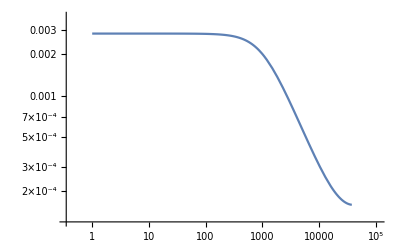

```mathematica
LogLogPlot[Abs[(1.5953160743351095*^9+ⅈ (88222.09697423488+(0.+1. ⅈ) s) s)/(5.60258269135162*^11+ⅈ (5.587511751578013*^8+(0.+1. ⅈ) s) s)],{s,1,37834.18499328932}]
```

```mathematica
37834.18499328932/(2Pi)
```

6021.5

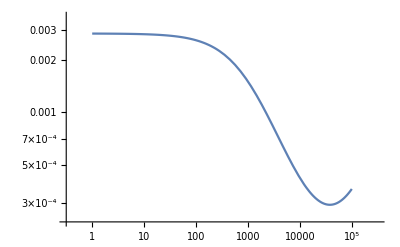

```mathematica
LogLogPlot[(1.5953160743351095*^9+s (88222.09697423488+1. s))/(5.60258269135162*^11+s (5.587511751578013*^8+1. s)),{s,1,100kk}]
```

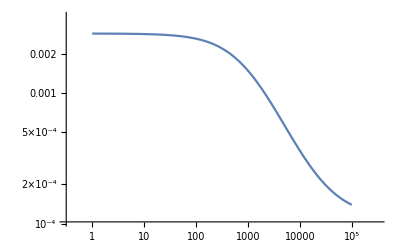

```mathematica
LogLogPlot[0.00011245561734989272+2.7425114898541256/(1002.7428199353631+1. s),{s,1,100kk}]
```

```mathematica
Z1
```

```mathematica
Zmod
```

(1.×10^15)/((1.×10^6+(1.×10^9)/s) s)

```mathematica
Z1
```

(1.×10^15)/((1.×10^6+(1.×10^9)/s) s)

```mathematica
(9.999999999999999*^14)/((1.*^6+(9.999999999999999*^8)/s) s)//FullSimplify
```

(1.×10^9)/(1000.+1. s)

```mathematica
R2
```

20500.